```mathematica
num2[n_]:=n/2
num1[n_]:=n
```

```mathematica
Limit[num2[n]-n,n->∞]
```

-∞

```mathematica
even[n_]:=n/2
whole[n_]:=n
```

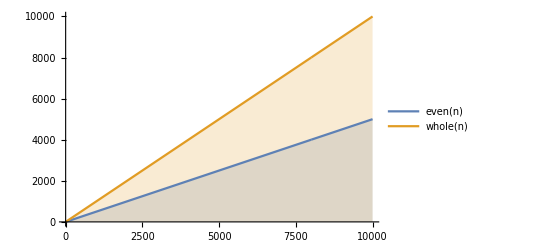

```mathematica
DiscretePlot[{even[n],whole[n]},{n,0,10000},PlotLegends->"Expressions"]
```

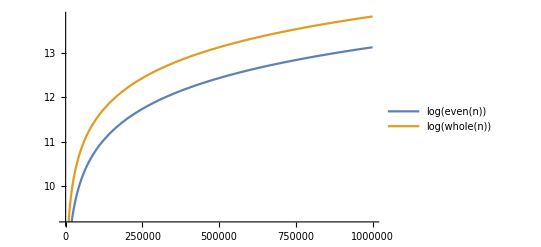

```mathematica
Plot[{Log[even[n]],Log[whole[n]]},{n,0,1000000},PlotLegends->"Expressions"]
```

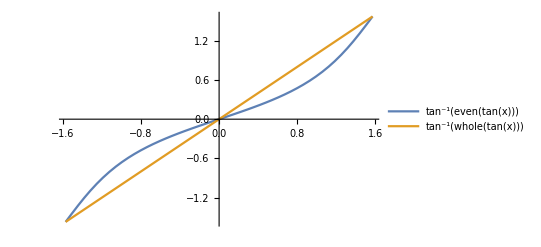

```mathematica
Plot[{ArcTan[even[Tan[x]]],ArcTan[whole[Tan[x]]]},{x,-π/2,π/2},PlotLegends->"Expressions"]
```

```mathematica
numZ[n_]:=n
numQ[n_]:=∞
```

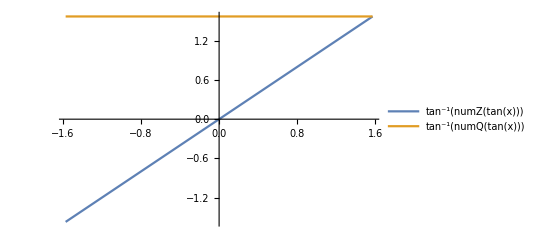

```mathematica
Plot[{ArcTan[numZ[Tan[x]]],ArcTan[numQ[Tan[x]]]},{x,-π/2,π/2},PlotLegends->"Expressions"]
```

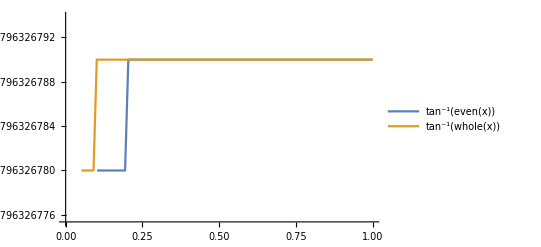

```mathematica
Plot[{ArcTan[even[x]],ArcTan[whole[x]]},{x,0,1000000000000},PlotLegends->"Expressions"]
```